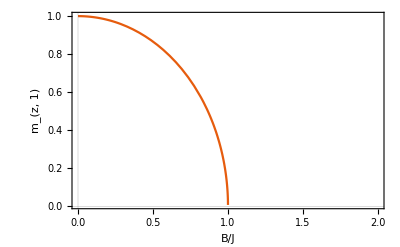

```mathematica
Plot[√(1-x^2),{x,0,2},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"B/J","m_(z, 1)"}]
```

```mathematica
Clear[J,z1,z2,B]
Manipulate[ListDensityPlot[values=Flatten[Table[{z1, z2, J z1 z2 - B(√(1-z1^2)+√(1-z2^2))},{z1,-1,1,0.025},{z2,-1,1,0.025}],1],PlotRange->Full,FrameLabel->{"m_(1, z)","m_(2, z)"},PlotLegends->Automatic,PlotLabel->TableForm[values[[Ordering[values[[;;,3]]][[;;2]]]],TableHeadings->{{"Dot 1", "Dot 2"},{"m_(1, z)","m_(2, z)","Energy"}}],Epilog->{Red,Point[values[[Ordering[values[[;;,3]]][[;;2]]]][[;;,;;2]]]}],{J,-1,1},{B,0,2}]
```

```mathematica
Clear[f,J,B,L,θ]
f[θ_]:=J ∑_(i=1)^(L-1) Cos[θ[i]]Cos[θ[i+1]]-B∑_(i=1)^L Sin[θ[i]]
```

```mathematica
J=-1;B=0.9;L=10;
```

```mathematica
Clear[θt]
r=RandomReal[];
Table[θt[i]= 2π ,{i,L}];
θgd[0]=θt;
```

```mathematica
Graphics3D[Table[Arrow[Tube[{{i,0,0}-(orig=0.5{Sin[θgd[0][i]],Cos[θgd[0][i]],0}),{i,0,0}+orig}]],{i,L}],Boxed->False,ViewPoint->Top,ViewProjection->"Orthographic"]
```

-Graphics3D-

```mathematica
Clear[gradf,θ]
gradf[θ_]=Table[D[f[θ],θ[i]],{i,L}];
```

```mathematica
Clear[η,θn]
η=0.1;
Nsteps=1000;
Do[
Table[θgd[n+1][i]=θgd[n][i]-η gradf[θgd[n]][[i]],{i,L}];
,{n,0,Nsteps}]
```

```mathematica
Manipulate[Graphics3D[Table[Arrow[Tube[{{i,0,0}-(orig=0.5{Sin[θgd[n][i]],Cos[θgd[n][i]],0}),{i,0,0}+orig}]],{i,L}],Boxed->False,ViewPoint->Top,ViewProjection->"Orthographic"],{n,0,Nsteps,1}]
```

```mathematica
Clear[h,J, B,val,vec]
h = J KroneckerProduct[PauliMatrix[3],PauliMatrix[3]] - B((σx1=KroneckerProduct[PauliMatrix[1],PauliMatrix[0]])+ (σx2=KroneckerProduct[PauliMatrix[0],PauliMatrix[1]]));
{val[J_,B_],vec[J_,B_]}=Eigensystem[h];
```

```mathematica
Inverse[vec[J,B]*.vec[J,B]ᵀ].(vec[J,B]*.h.vec[J,B]ᵀ)//ComplexExpand//FullSimplify
```

{{-J,0,0,0},{0,J,0,0},{0,0,-√(4 B^2+J^2),0},{0,0,0,√(4 B^2+J^2)}}

```mathematica
Inverse[vec[J,B]*.vec[J,B]ᵀ].(vec[J,B]*.σx1.vec[J,B]ᵀ)//ComplexExpand//FullSimplify
```

{{0,-1,0,0},{-1,0,0,0},{0,0,(2 B)/(√(4 B^2+J^2)),(J (1-J/(√(4 B^2+J^2))))/(2 B)},{0,0,(J (1+J/(√(4 B^2+J^2))))/(2 B),-(2 B)/(√(4 B^2+J^2))}}

```mathematica
Manipulate[{(v*.KroneckerProduct[PauliMatrix[3],PauliMatrix[0]].v)/(v*.v),(v*.KroneckerProduct[PauliMatrix[0],PauliMatrix[3]].v)/(v*.v)}//ComplexExpand//FullSimplify,{v,vec[J,B]}]
Manipulate[{(v*.σx1.v)/(v*.v),(v*.σx2.v)/(v*.v)}//ComplexExpand//FullSimplify,{v,vec[J,B]}]
```

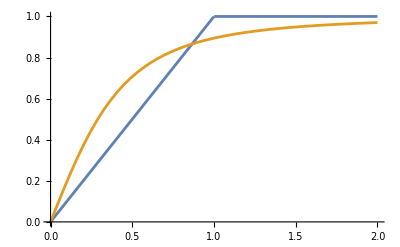

```mathematica
Plot[{Min[B,1],(2 B)/(√(4 B^2+1))},{B,0,2}]
```

```mathematica
Manipulate[Plot[(1/2{1,1,1,1}.v/Norm[v])/.J->1,{B,0,10},PlotRange->Full],{v,vec[J,B]}]
```